# 1-D Conductión across a Tube “Finite Difference Equation”

In this notebook we are going to resolve the temperature distribution on a pipeline.
At the north boundary we have a constant flow heat, At the south boundary it is a fluid; whose thermal field is a lineal distribution. The west boundary is adiabatic and finally we have a known temperature at the east.

## Data And Control Parameters

The initial conditions, the geometric data and the physics properties of the material (pipeline) and the fluid are here (coefficient of convection, conduction, ambient temperature, temperature distribution of the fluid, specific heat).

You can control al the different parameters; and the temperature distribution over the cupper is going to change. Also you can change the dimensions of the pipeline; Length, Thick (external ”N” and internal diameter “S”).

Also the most interesting parameter to change is the number of nodes, so you can visualize with more precision the temperature distribution in the  pipeline.

```mathematica
qW=0;(*Adiabatic West boundary Units: W*)
tempE=25;(*Temperature East boundary Units .baC--YOU CAN CHANGE*)
qN=1000;(*Heat North boundary   W/m^2--YOU CAN CHANGE*)
a=5;(*Constant linear fluid distribution "Slope"--YOU CAN CHANGE*)
b=10;(*Constant linear fluid distribution "y-axis intercept"--YOU CAN CHANGE*)
αS=100;(*Convection coeficient Units:W/(m^2 .baC)*)
diamS=0.007; (*Diameter first boundary Units: m^2--YOU CAN CHANGE*)
areaS=(Pi diamS^2)/4;(*Area first boundary Units: m*)
perS=Pi diamS;(*Perimeter Units: m*)
diamN=0.01;(*Diameter second boundary Units:--YOU CAN CHANGE m*)
areaN=(Pi diamN^2)/4;(*Area second boundary Units:  m^2*)
perN=Pi diamN;(*Perimeter Units: m*)
areaEffect=areaN-areaS;
L=1;(*Pipeline Lenght Units: m--YOU CAN CHANGE*) 
λp=400;(*Pipeline Conductivity W/(m .baC)*) 
Cpt=400;(*Fluid Specific Heat J/(kg .baC)*) 
nodes=200;(*--CHANGE EVERY TIME YOU COMPILE THE WHOLE PROGRAM TO SEE MORE NODES OR LESS*)
distNodes=L/(nodes-1);(*Distance between nodes*)
```

## Fluid thermic Field

The initial conditions, the geometric data and the coefficient of convection are here.

Direction/Caption: In a single line, say what the code that follows will do. End this line with a colon (e.g. “Make a map of Portugal:”)

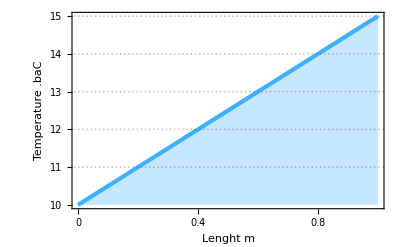

```mathematica
Ts[z_]:=a z+b
Plot[Ts[z],{z,0,L},Filling->Axis,PlotTheme->"Business",PlotStyle->96,FrameLabel->{"Lenght m","Temperature .baC"}]
Table[Ts[z],{z,0,L,distNodes}]//N;
```

From here you are going to resolve a problem of energy transmisión around the pipeline. This happened because there are a temperature difference between the pipeline, the fluid, the surroundings and the heat transmission form North part of the pipeline.

The mechanism of heat transmission we are modeling is 1-D heat conduction, and we are going to use a numeric method for resolve it and the way we are going to discretize the governing equations is called FDE (“finite difference equations”).

## Nodes Discretization

In this par we are just putting on the right position each node so we can discretize the FDE based on energy balance over the pipeline

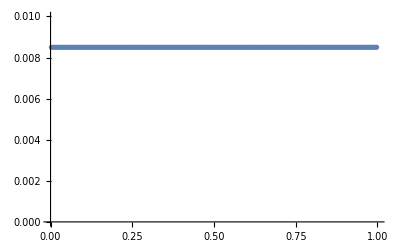

```mathematica
distNodes=L/(nodes-1);(*Distance between nodes*)
volx=Range[0,L,distNodes];
posx= Table[(volx[[i]]+volx[[i+1]])/2,{i,1,nodes-1}];
posy=Table[(diamN+diamS)/2,nodes-1];
pos=Flatten[Table[{posx[[i]],posy[[i]]},{i,1,nodes-1}],0];(*position x,y of nodes*)
ListPlot[pos, PlotRange->{{0,1},{0,diamN}}]
```

## Characteristic Nodes and Control Volumes

The first square show the Area of conduction and the Perimeters where heat conductive transfer occurs. The second square shows the properties of the balance of energy with de node of interest (p) with the boundary north and south (d); and the nodes west (c) and east (b).

## Numerical Procedure

The magic of the “FDE” method is like you don’t need to use the differential equations (Fourier Law “Conduction”, Newton cooling Act “Convection” to resolve a heat transfer problem). You use algebraic equations (Fourier Law -> Q=A λ/Δx(T2-T1) 
Newton cooling->Q=α A (T2-T1) ).

Once than you realize the energy balance on the characteristic nodes you are going to have an equation like this:

```mathematica
For the first node
Subscript[Q, W]+Subscript[Q, S]=Subscript[Q, E]+Subscript[Q, N]
0+α A^(Tαf-Tp)=A λ/Δx(Tp-Te)+Subscript[Q, N]
Doing the algebra

Tp (α A+A λ/Δx)=Te (A λ/Δx)+(Tαf ) α A+Subscript[Q, N]
Where 
(α A+A λ/Δx)=a1
(A λ/Δx)=b1
0=c1
(Tαf ) α A+Subscript[Q, N]=d1

 Realizing this procedure to the other characteristic nodes we obtain the next matrix for the basic case of 3 nodes

({{a1, b1, 0}, {c2, a2, b2}, {0, c3, a3}})({{d1}, {d2}, {d3}})=({{T1}, {T2}, {T3}})
So know we have lineal sistem TDMA "Tridiagonal matrix" and we resolve aplying this method:

    P=b/(a - c P[i-1])
	Q=(d + c  Q [i-1])/(a - c  P [i-1])
To finally obtain the distribution temperature

T[i]=P [i]  T[i+1]+Q [i]
```

Realizing a energy balance over each characteristic node we obtain the results of the abcd coefficients .

```mathematica
(*First Characteristic node*)
ap[1]= (areaEffect λp)/distNodes+ (αS perS distNodes)/2;
bE[1]=(areaEffect λp)/distNodes;
cW[1]=0;
d[1]=(qN perS distNodes)/2+(αS perS distNodes)/2 Ts[0];

(*Second Characteristic node*)
ap[2]= (2areaEffect λp)/distNodes+αS perS distNodes;
bE[2]=(areaEffect λp)/distNodes;
cW[2]=(areaEffect λp)/distNodes;


(*Third Characteristic node*)
ap[3]=1;
bE[3]=0;
cW[3]=0;
d[nodes-1]=tempE;
```

### Forming TDMA “Tridiagonal Matrix”

```mathematica
MT[n_]:=MT[n]=Normal[
SparseArray[
{{1,1}->ap[1],{1,2}->bE[1],
{n,n-1}->cW[3],{n,n}->ap[3],
Band[{1,1}]->ap[2],Band[{1,2}]->bE[2],Band[{2,1}]->cW[2]},
n]];
MT[nodes-1]//MatrixForm;
dtot={};(*This d change with the temperature of the fluid, because the convective heat transfer is function of the fluid temperature *)
d[i_]:=qN perN distNodes+αS perS distNodes Ts[distNodes(i-1)];
dtot=Join[{d[1]}, Table[d[i],{i,2,nodes-2,1}], {d[nodes-1]}];
```

### Resolving TDMA for P and Q

```mathematica
Ptot={};
Qtot={};
Ptot={(MT[nodes-1][[1,1+1]])/(MT[nodes-1][[1,1]])};(*This is Ptot=b1/a1, because c=0*)
Do[
(*This is Ptot=b2/(a2 - c2 Ptot[i-1]), the general equation *)
P=MT[nodes-1][[i,i+1]]/(MT[nodes-1][[i,i]]-MT[nodes-1][[i,i-1]] Ptot[[i-1]]);

AppendTo[Ptot,P],
{i,2,nodes-2,1}
];
    AppendTo[Ptot,0];(*Last Ptot=0 because b3 (last)=0*)
Qtot={dtot[[1]]/(MT[nodes-1][[1,1]])};(*This is Ptot=d1/a1, because c=0*)
Do[
(*This is Qtot=(d2 + c2 Qtot[i-1])/(a2 - c2 Ptot[i-1]), the general equation *)
Q=(dtot[[i]]+MT[nodes-1][[i,i-1]] Qtot[[i-1]])/(MT[nodes-1][[i,i]]-MT[nodes-1][[i,i-1]]Ptot[[i-1]]);AppendTo[Qtot,Q],
{i,2,nodes-1,1}
];
```

### Temperatures Distribution

With Qtot and Ptot we can calculate the distribution of temperature for the first iteration...The program is not complete...

```mathematica
T[nodes-1]=Qtot[[nodes-1]];
T[i_]:=Ptot[[i]]T[i+1]+Qtot[[i]]
T1=T/@Reverse[Range[nodes-1]];
```

The firs values of this list is the temperature of the last node, and the last value is the temperature from the first node.
This process don’t need to be iterative because the physical properties don’t depend of the initial temperature. Otherwise we need to propose an initial distribution a temperatures and refresh it with the calculate ones.

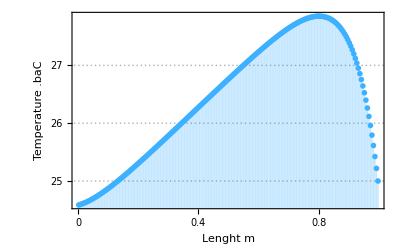

```mathematica
tempNum=Reverse[T1];
temp=ListPlot[
Table[
	{posx[[i]],tempNum[[i]]},
	{i,1,Length[posx]}
	],
Filling->Axis,
PlotTheme->"Business",
PlotStyle->96,
FrameLabel->{"Lenght m","Temperature .baC"}]
```

Finally you can evaluate this notebook changing the number of nodes, to whatever value you deserve (not less than 3).

This method could apply to 1-D, 2-D and 3-D heat transfer systems. 
This is a example of a 2-D heat dissipator who resolve it with the same method using 6 characteristic methods.

Further Explorations

TDMA
Gauss-Sieddel Iteration

Heat Transfer on a pipeline

Authorship information

Rubén García Soriano

21/06/2017

rugas@ier.unam.mx